```mathematica
(*Position of the lost plan*)
distantR = 0.8;

(*
	The position where the plane actually is lost at
	The plane start getting missing at {0,0}
*)
lostX = distantR*Cos[0.5];
lostY = distantR*Sin[0.5];

(*stepDist is the *)
stepDist=0.05;

(*Prec is the range when the object is likely to bedescivered*)
prec = stepDist/2;

(*Range*)
rangeX={-1,1};
rangeY={-1,1};

(*Minimal Probability possible*)
(*minP=1/((rangeX[[2]]-rangeX[[1]])*((rangeY[[2]]-rangeY[[1]]))/stepDist^2*10000);*)
minP=0;

(*Function that change from a position to an index*)
indexOf[x_,y_]:=Module[{},
{Round[(x-(rangeX[[1]]))/stepDist]+1,Round[(y-(rangeY[[1]]))/stepDist]+1}
];

lostIndexP=indexOf[lostX,lostY];
lostIndexX=lostIndexP[[1]];
lostIndexY=lostIndexP[[2]];
```

```mathematica
(*Print Function*)
(*temp = PrintTemporary[INITIALIZED];
(*myPrint[x_]:=Module[{},];*)
For[i=0,i<10,i++,NotebookDelete[temp];temp = PrintTemporary[i];Pause[999];]*)
```

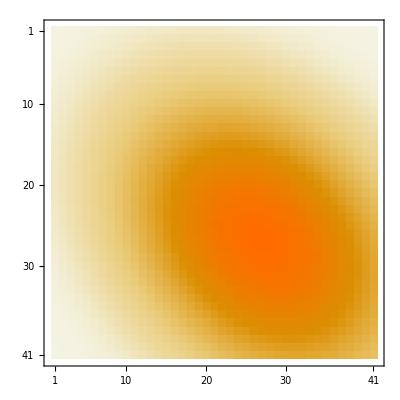
{-Graphics3D-,-Graphics-,Null}

```mathematica
(* 
	searcher data is the probability density of the 
	probability that the searcher can find the object
	given that the object is in the position
	P(D|O)
*)
searcherData={};

(* {cx,cy} is the initial center of the searcher *)
(* precondition:  0<ρ<1 *)
searcherDataInit[x_,y_]:=Module[{
centerX=0.3,centerY=0.3,
ρ=0.3,σx=0.5,σy=0.5
},
PDF[MultinormalDistribution[{centerX,centerY},{{σx^2,ρ*σx*σy},{ρ*σx*σy,σy^2}}],{x,y}]*stepDist^2
(*a= Abs[(x-rangeX[[1]])/stepDist]*10;
b=Abs[(y-rangeY[[1]])/stepDist]*10;
PDF[MultivariatePoissonDistribution[1,{2,3}],{a,b}]*)
(*PDF[BinormalDistribution[1/3],{x,y}]*)
];

searcherData= Table[
searcherDataInit[x,y],
{x,rangeX[[1]],rangeX[[2]],stepDist},
{y,rangeY[[1]],rangeY[[2]],stepDist}
];
{
DiscretePlot3D[searcherDataInit[x,y],{x,rangeX[[1]],rangeX[[2]],stepDist},{y,rangeY[[1]],rangeY[[2]],stepDist},ExtentSize->stepDist],
MatrixPlot[searcherData],
(*searcherData*)
}
```

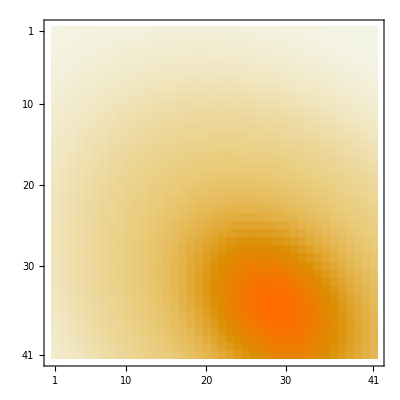
{-Graphics3D-,-Graphics-}

```mathematica
(*
	data is the probability density of the 
	probability that if the object is in a
	particular position
	P(O)
*)
objectData = {};

(* precondition:  0<ρ<1 *)
objectDataInit[x_,y_]:=Module[{ρ=0.3,σx=0.3,σy=0.3},
PDF[MultinormalDistribution[{lostX,lostY},{{σx^2,ρ*σx*σy},{ρ*σx*σy,σy^2}}],{x,y}]*stepDist^2
];

objectData=Table[
objectDataInit[x,y],
{x,rangeX[[1]],rangeX[[2]],stepDist},
{y,rangeY[[1]],rangeY[[2]],stepDist}
];
{
DiscretePlot3D[objectDataInit[x,y],{x,rangeX[[1]],rangeX[[2]],stepDist},{y,rangeY[[1]],rangeY[[2]],stepDist},ExtentSize->stepDist],
MatrixPlot[objectData]
}
```

0.000915647

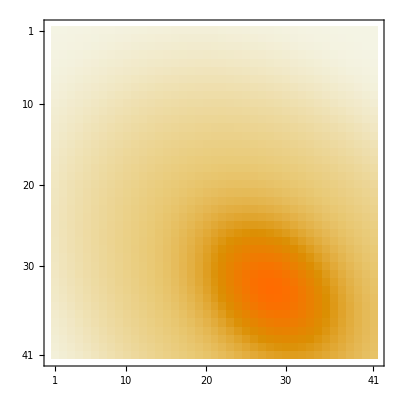
{-Graphics-,-Graphics-,-Graphics-}

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(* 
	data is the probability density of the 
	probability that if the object is in the position
	and given that we can detected it
	P(D|O)*P(O)=P(O|D)
*)
data = {};

(*Generate density distrybution*)
dataGenerate[x_,y_]:=Module[{xp=indexOf[x,y][[1]],yp=indexOf[x,y][[2]]},
searcherData[[xp]][[yp]]*
objectData[[xp]][[yp]]
];

(*Generate the Initial Data*)
data = searcherData*objectData;
MatrixForm[data];
Apply[Plus,Flatten[data]]
{MatrixPlot[data],MatrixPlot[objectData],MatrixPlot[searcherData]}
{ListPlot3D[data,PlotRange->All],ListPlot3D[objectData,PlotRange->All],ListPlot3D[searcherData,PlotRange->All]}
```

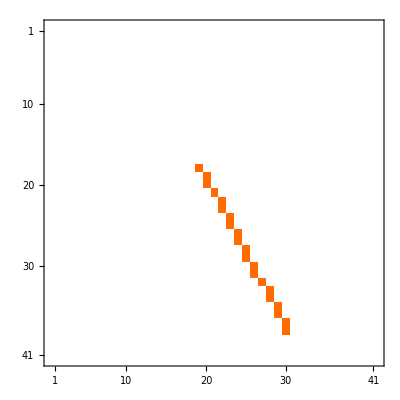
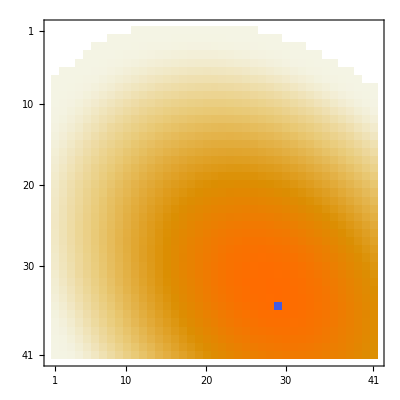
{-Graphics-,-Graphics-,-Graphics-,{0.702066,0.38354}}

```mathematica
(*Simulation Environment*)
(*If the position(x,y) is on the path*)
isOnPath[x_,y_]:=Module[{m=lostY/lostX, expT=prec},
(*Linear Path*)
Abs[x-0]+Abs[x-Cos[ArcTan[m]]*distantR]-1<expT && 
Abs[y-m*x] <expT
];

(*Whether the position is the plane position*)
isFound[x_,y_]:=Module[{rt = prec,lp,lx,ly},
lp=indexOf[x,y];
lx=lp[[1]];
ly=lp[[2]];
lostIndexX==lx && lostIndexY==ly
];

(* The probability that we give evidence when searching at the path*)
pEvidenceFoundOnPath=0.3;

(*Search a particular Point in the map*)
searchMapAtPoint[x_,y_]:=Module[{p=RandomReal[{0,1}] < pEvidenceFoundOnPath},
isOnPath[x,y] && p
];

(*Update the Data At Specific Point*)
changeDataAt[list_,posX_,posY_,newValue_]:=Module[{expT=prec},
Table[
If[
Abs[posX-x]< expT &&Abs[posY-y]<expT,
newValue,
data[[
indexOf[x,y][[1]]
]][[
indexOf[x,y][[2]]
]]
],
{x,rangeX[[1]],rangeX[[2]],stepDist},
{y,rangeY[[1]],rangeY[[2]],stepDist}
]
];
planePathData = Table[If[isOnPath[x,y],1,0],{x,-1,1,stepDist},{y,-1,1,stepDist}];

plotLostPlane= changeDataAt[data,lostX,lostY,-100];
{
(*ListDensityPlot[planePathData,PlotRange->All],
ListDensityPlot[data,PlotRange->All],*)
MatrixPlot[planePathData,PlotRange->All],
MatrixPlot[plotLostPlane,PlotRange->All],
MatrixPlot[data,PlotRange->All],
{lostX,lostY}
}
```

```mathematica
(* Updates the object probability at position (x,y) when unfound *)
failSearchProbability[x_,y_]:=Module[{
ix=indexOf[x,y][[1]], iy=indexOf[x,y][[2]],
poo=0,pdo=0,ret
},
poo=objectData[[ix]][[iy]];
pdo=searcherData[[ix]][[iy]];
ret=(poo*Abs[1-pdo])/(1-poo*pdo);
If[ret<minP,minP,ret]
];
tx=RandomReal[{-1,1}];
ty=RandomReal[{-1,1}];
testPos=indexOf[tx,ty];
For[i=0,i<20,i++,If[objectData[[testPos[[1]]]][[testPos[[2]]]]-failSearchProbability[tx,ty]<0,False]
]
```

```mathematica
(* Updates the object probability at position(x,y) unsearched *)
failUnsearchProbability[x_,y_,xo_,yo_]:=Module[{
ix=indexOf[x,y][[1]], iy=indexOf[x,y][[2]],
ixo=indexOf[xo,yo][[1]], iyo=indexOf[xo,yo][[2]],
poo=0,pdo=0,qoo=0,ret
},
qoo=objectData[[ix]][[iy]];
poo=objectData[[ixo]][[iyo]];
pdo=searcherData[[ixo]][[iyo]];
ret =(qoo/(1-poo*pdo));
If[ret<minP,minP,ret]
];

tx=RandomReal[{-1,1}];
ty=RandomReal[{-1,1}];
testPos=indexOf[tx,ty];
For[i=0,i<20,i++,If[objectData[[testPos[[1]]]][[testPos[[2]]]]-failUnsearchProbability[tx,ty]>0,False]
]
```

```mathematica
(* Update the data for each fail position*)
updateFail[x_,y_]:=Module[{expT=prec,originalObjData,originalData},
originalObjData=objectData;
objectData=Table[
If[
Abs[posX-x]< expT &&Abs[posY-y]<expT,
failSearchProbability[posX,posY],
failUnsearchProbability[posX,posY,x,y]
],
{posX,rangeX[[1]],rangeX[[2]],stepDist},
{posY,rangeY[[1]],rangeY[[2]],stepDist}
];
originalData = data;
data =objectData*searcherData;
(*Save the testing information*)
{
(*MatrixPlot[originalObjData],
MatrixPlot[originalData],*)
MatrixPlot[originalObjData-objectData],
MatrixPlot[originalData-data],
MatrixPlot[objectData],
MatrixPlot[data],
{x,y}
}
];
{MatrixPlot[data],ListPlot3D[data]}
```

{-Graphics-,-Graphics3D-}

```mathematica
(* Found the next search point *)
maxIndexP={0,0};
nextSearchPoint[list_]:=Module[{
max=-Infinity,
x=rangeX[[1]], y=rangeY[[1]],
mx=0,my=0
},
While[x-rangeX[[2]] < prec,
While[y-rangeY[[2]] < prec,
ix=indexOf[x,y][[1]];
iy=indexOf[x,y][[2]];
If[
max<list[[ix]][[iy]],
max=list[[ix]][[iy]];
mx=x;
my=y;
];
y+=stepDist;
];
y=rangeY[[1]];
x+=stepDist;
];
Return[{mx,my}];
];
```

```mathematica
Total[{0,0}]
```

0

False

Fount

{0.6,0.35}

False

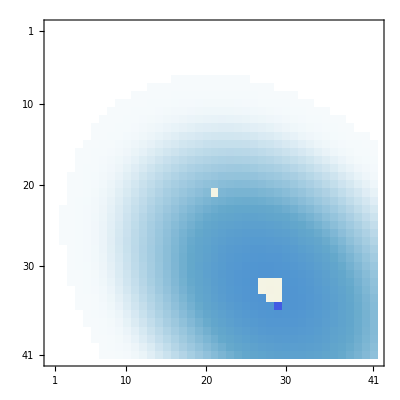
{-Graphics-,-Graphics-,-Graphics-,{0.702066,0.38354},{35,29}}

```mathematica
(*
	Search till found
	x_,y_:starting position
	r_:searching raius
*)
searchPath={};
startSearching[x_,y_]:=Module[{cx=x,cy=y,p,n,print},
n=0;
print={};
Monitor[
While[(!isFound[cx,cy])&&n<100,
n+=1;
(*update the map*)
print=updateFail[cx,cy];

(*Define the next point*)
p=nextSearchPoint[data];
cx=p[[1]];
cy=p[[2]];
searchPath= Append[searchPath,{cx,cy}];
],{print,n}];
Print["Fount"];
Return[{cx,cy}]
];
isFound[0.3,0.3]
result=startSearching[0,0]
isFound[result[[1]],result[[2]]]
{
(*ListDensityPlot[planePathData,PlotRange->All],
ListDensityPlot[data,PlotRange->All],*)
MatrixPlot[planePathData,PlotRange->All],
MatrixPlot[plotLostPlane,PlotRange->All],
MatrixPlot[plotLostPlane-data,PlotRange->All],
{lostX,lostY},
{lostIndexX,lostIndexY}
}
(*ListDensityPlot[data,PlotRange->All]*)
(*{ListPlot[searchPath]}
MatrixPlot[data]*)
```